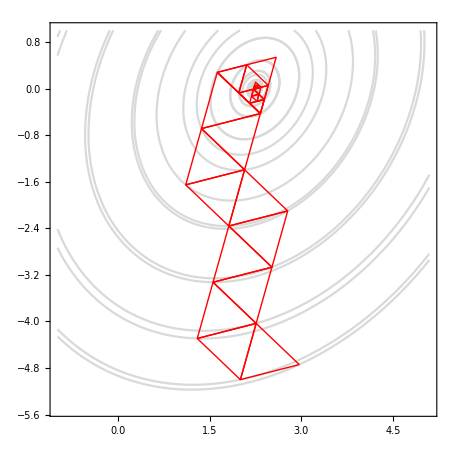

{31,70}

{2.23757,-0.000508835}

-66.

{60,150}

{2.23607,-3.75247×10^-6}

-66.

{{30,106},{3,-5,2,-5,3,-4},{2,-5,3,-4,1.5,-3.5},{3,-4,1.5,-3.5,2.75,-1.25},{1.5,-3.5,2.75,-1.25,1.25,-0.75},{2.75,-1.25,2.5,1.5,1.25,-0.75},{2.5,1.5,1.25,-0.75,2.3125,-0.4375},{1.25,-0.75,2.14063,0.453125,2.3125,-0.4375},{3.20313,0.765625,2.14063,0.453125,2.3125,-0.4375},{1.73828,-0.371094,2.14063,0.453125,2.3125,-0.4375},{2.71484,0.386719,2.14063,0.453125,2.3125,-0.4375},{2.14063,0.453125,2.3125,-0.4375,1.98242,-0.181641},{2.14063,0.453125,2.3125,-0.4375,2.4707,0.197266},{2.3125,-0.4375,2.4707,0.197266,2.26611,0.166504},{2.4707,0.197266,2.34045,-0.127808,2.26611,0.166504},{2.34045,-0.127808,2.13586,-0.158569,2.26611,0.166504},{2.13586,-0.158569,2.26611,0.166504,2.13126,0.0698547},{2.13586,-0.158569,2.26611,0.166504,2.27072,-0.0619202},{2.33469,0.157723,2.26611,0.166504,2.27072,-0.0619202},{2.26611,0.166504,2.27072,-0.0619202,2.20214,-0.0531387},{2.27072,-0.0619202,2.20214,-0.0531387,2.25127,0.0544872},{2.20214,-0.0531387,2.2047,0.0319715,2.25127,0.0544872},{2.20214,-0.0531387,2.25127,0.0544872,2.24871,-0.030623},{2.27392,0.0444676,2.25127,0.0544872,2.24871,-0.030623},{2.25127,0.0544872,2.24871,-0.030623,2.22607,-0.0206033},{2.24871,-0.030623,2.22607,-0.0206033,2.24433,0.0144371},{2.22168,0.0244567,2.22607,-0.0206033,2.24433,0.0144371},{2.22607,-0.0206033,2.24196,-0.016853,2.24433,0.0144371},{2.22607,-0.0206033,2.22844,0.0106868,2.24433,0.0144371},{2.22844,0.0106868,2.24433,0.0144371,2.23123,-0.00402069},{2.24433,0.0144371,2.24712,-0.000270432,2.23123,-0.00402069}}

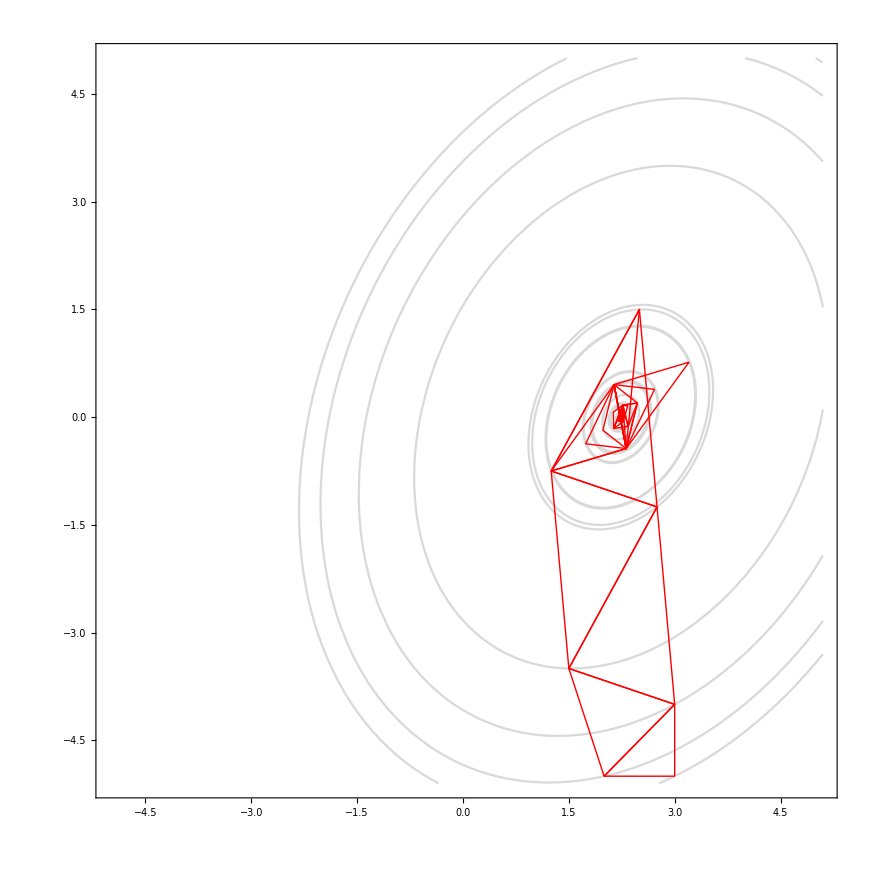

{30,106}

{2.24089,0.00338198}

-65.9998

{71,246}

{2.23607,1.4543×10^-6}

-66.

```mathematica
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f1p1.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-1,5.1},{y,-5.5,1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f1p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f1p1.txt","Table"]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-5,5.1},{y,-5.1,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f1p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
```

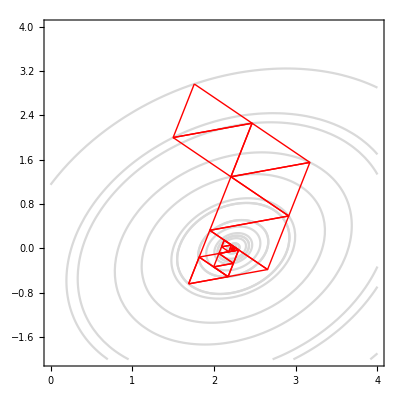

{24,63}

{2.23618,0.00718525}

-65.9996

{54,143}

{2.23607,2.07795×10^-6}

-66.

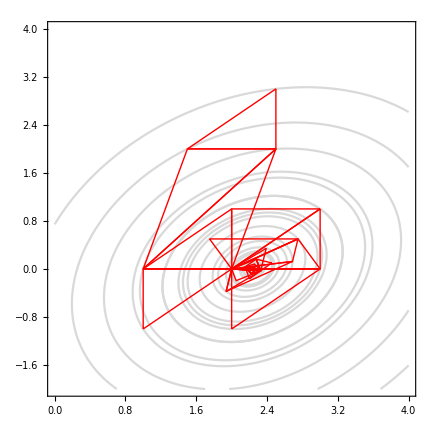

{31,106}

{2.23544,0.00126}

-66.

{66,234}

{2.23607,-2.35862×10^-6}

-66.

```mathematica
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f1p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-2,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]

p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f1p2.txt","Table"];
str[[1]]

points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f1p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,0,4},{y,-2,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]

p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f1p2.txt","Table"];
str[[1]]

points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F1[p[[1]],p[[2]]]
```

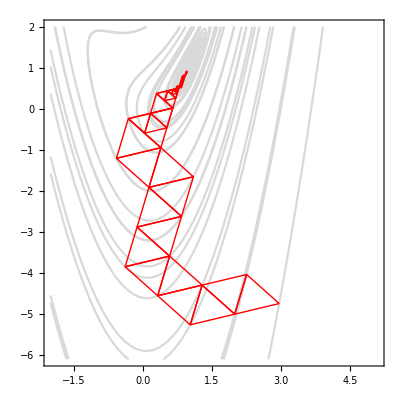

{60,107}

{0.958776,0.908309}

0.00181916

{224,354}

{0.999947,0.999879}

3.00298×10^-9

{{34,111},{3,-5,3,-4,2,-5},{3,-4,2,-5,1.5,-3.5},{2,-5,1.5,-3.5,0.5,-4.5},{1.5,-3.5,0.5,-4.5,0,-3},{-1,-4,0.5,-4.5,0,-3},{0.5,-4.5,0.875,-3.625,0,-3},{0.875,-3.625,0,-3,0.3125,-0.9375},{0,-3,-0.5625,-0.3125,0.3125,-0.9375},{-0.25,1.75,-0.5625,-0.3125,0.3125,-0.9375},{-0.25,1.75,0.3125,-0.9375,1.21875,1.84375},{1.27344,-0.195313,0.3125,-0.9375,1.21875,1.84375},{0.257813,1.10156,0.3125,-0.9375,1.21875,1.84375},{0.3125,-0.9375,1.01953,0.128906,1.21875,1.84375},{1.92578,2.91016,1.01953,0.128906,1.21875,1.84375},{1.01953,0.128906,0.71582,0.0244141,1.21875,1.84375},{0.915039,1.73926,0.71582,0.0244141,1.21875,1.84375},{0.71582,0.0244141,0.993408,0.531494,1.21875,1.84375},{1.49634,2.35083,0.993408,0.531494,1.21875,1.84375},{0.993408,0.531494,1.21875,1.84375,0.91095,0.606018},{1.21875,1.84375,1.10057,1.57158,0.91095,0.606018},{1.10057,1.57158,0.79277,0.333847,0.91095,0.606018},{0.79277,0.333847,0.91095,0.606018,0.976215,1.02076},{0.91095,0.606018,1.0944,1.29293,0.976215,1.02076},{1.0944,1.29293,0.976215,1.02076,0.973127,0.88143},{0.91481,0.780176,0.976215,1.02076,0.973127,0.88143},{0.976215,1.02076,0.973127,0.88143,1.03453,1.12201},{0.973127,0.88143,1.03453,1.12201,1.01764,0.992202},{0.973127,0.88143,1.03453,1.12201,0.990023,1.01124},{1.03453,1.12201,0.990023,1.01124,0.992703,0.974027},{0.969778,0.927944,0.990023,1.01124,0.992703,0.974027},{0.990023,1.01124,1.00216,1.02498,0.992703,0.974027},{1.00484,0.987766,1.00216,1.02498,0.992703,0.974027},{1.00216,1.02498,0.993726,1.00537,0.992703,0.974027},{1.00216,1.02498,0.992703,0.974027,1.00113,0.993634}}

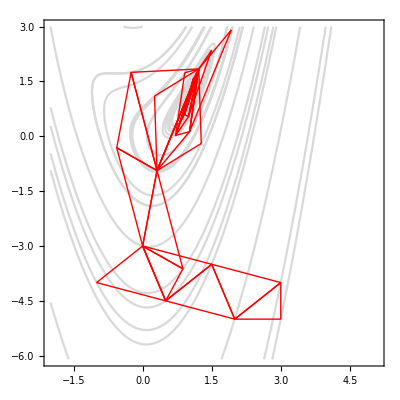

{34,111}

{0.998663,0.997546}

1.83438×10^-6

{75,249}

{1.,1.}

2.29212×10^-11

```mathematica
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f2p1.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2,5.1},{y,-6.1,2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f2p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f2p1.txt","Table"]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2,5.1},{y,-6.1,3},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f2p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
```

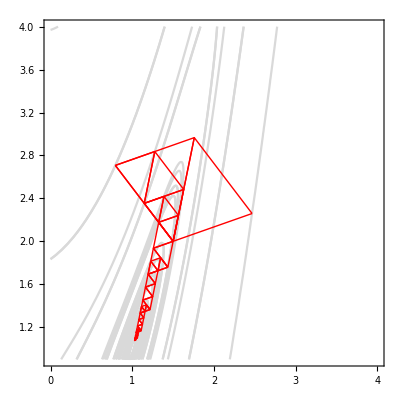

{41,85}

{1.03439,1.0814}

0.00131334

{177,298}

{1.00004,1.0001}

2.02307×10^-9

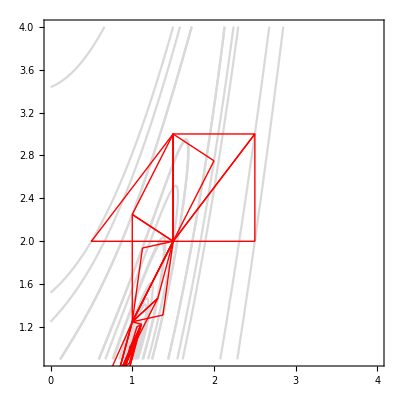

{29,97}

{0.999576,1.00231}

0.0000101634

{68,234}

{0.999999,0.999999}

3.22222×10^-13

```mathematica
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f2p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0,4},{y,0.9,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]

p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f2p2.txt","Table"];
str[[1]]

points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f2p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0,4},{y,0.9,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]

p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f2p2.txt","Table"];
str[[1]]

points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
```

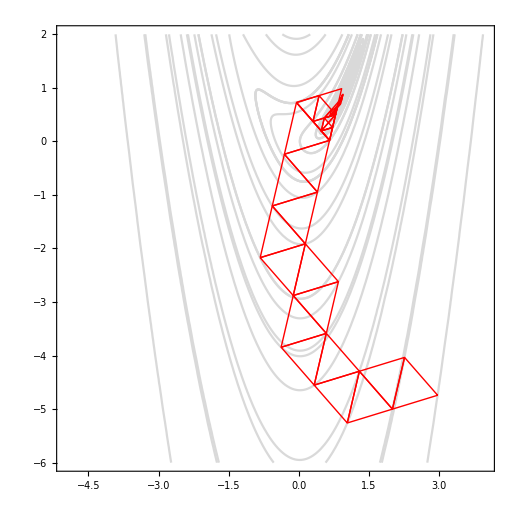

{48,95}

{0.934247,0.869049}

0.00433766

{336,480}

{0.999923,0.999841}

5.89616×10^-9

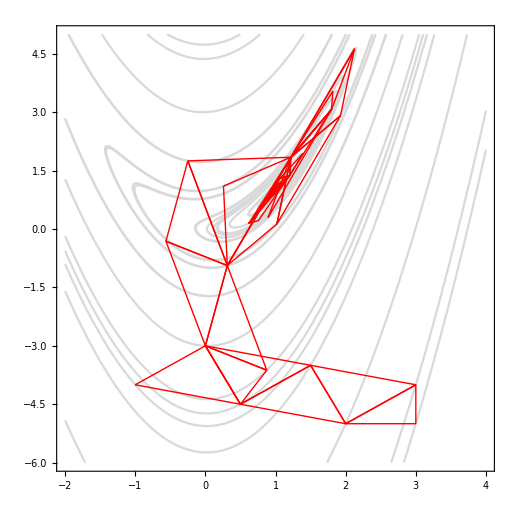

{41,129}

{0.996321,0.997215}

0.0000343242

{82,268}

{1.00001,1.00001}

4.226×10^-11

```mathematica
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f3p1.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-5,4},{y,-6,2},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f3p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f3p1.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2,4},{y,-6,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f3p1.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
```

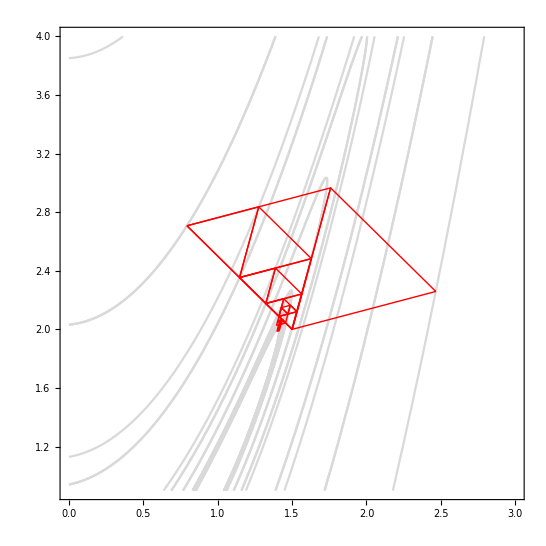

{27,67}

{1.40478,1.99316}

0.164234

{1097,1388}

{1.00022,1.00046}

5.00542×10^-8

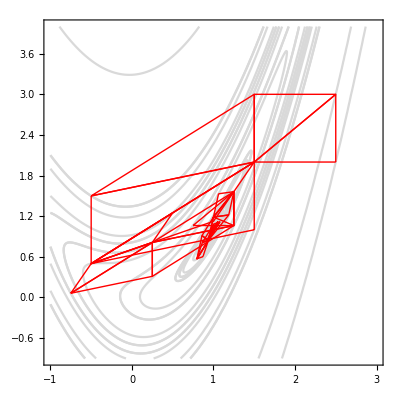

{33,116}

{0.990014,0.979462}

0.000100157

{72,239}

{0.999994,0.999986}

4.37379×10^-11

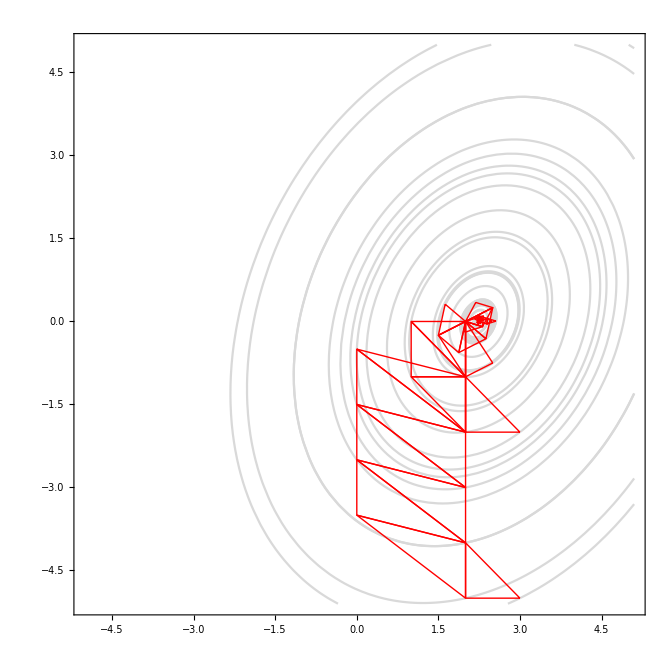

{43,122}

{2.23283,-0.0192642,2.2493,-0.00286675,2.24023,0.00292969}

{2.24079,-0.00640043}

-65.9994

{89,253}

{2.23665,0.000160873,2.23572,-0.0000452386,2.23573,-0.0000522515}

{2.23603,0.0000211276}

-66.

```mathematica
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps1f3p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0,3},{y,0.9,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/RegSimplexeps2f3p2.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps1f3p2.txt","Table"];
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-1,3},{y,-0.9,4},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Red,Line[{points1[[i]],points2[[i]],points3[[i]],points1[[i]]}]}],{i,1,Length[points1]}];
Show[K,M]
str[[1]]
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
str=Import["D:/1/MOVI lab/lab7/lab7/Simplexeps2f3p2.txt","Table"];
str[[1]]
points1=Table[{str[[i,1]],str[[i,2]]},{i,2,Length[str]}];
points2=Table[{str[[i,3]],str[[i,4]]},{i,2,Length[str]}];
points3=Table[{str[[i,5]],str[[i,6]]},{i,2,Length[str]}];
p=(points1[[Length[points1]]]+points3[[Length[points1]]]+points2[[Length[points1]]])/3
F2[p[[1]],p[[2]]]
```